# Dynamical Systems in Cosmology

#### Presenter: Janna May Angeles

### Objectives:

• Introduce the Friedmann-Robertson-Walker (FRW) cosmology
• Apply the method of dynamical systems

## What is Cosmology?

Simply put, it is the study of the formation and evolution of the Universe.

We refer here to modern cosmology which took shape with the observations on the expansion of the Universe by Hubble in 1929  and on the cosmic microwave background (CMB) radiation by Penzias and Wilson in 1965.

-Graphics-

### The ΛCDM model

This is the standard model in cosmology due to its fairly successful predictions in comparison to observations. In this model, the universe is composed of ~ 70% dark energy, ~25% dark matter, and ~5% ordinary matter + radiation. Its expansion history can be roughly summarized by

inflation → radiation-dominated → ordinary matter-dominated → dark energy-dominated

This model is characterized by Einstein’s general relativity and FRW equations.

## Friedmann-Robertson-Walker (FRW) Cosmology

### The cosmological principle

“Over large distances (~100 Mpc or more), the universe will look homogeneous and isotropic whichever way one looks at it.”

Homogeneity - same at every location
Isotropy - same at every direction

-Graphics- | Homogeneity and isotropy (img src: http://abyss.uoregon.edu/~js/cosmo/lectures/lec05.html)

-Graphics- | Left: a pattern that is anisotropic, but is homogenous on scales larger larger than the stripe width. Right: a pattern that is isotropic about the origin, but is inhomogeneous. (img src: Ryden, B., Introduction to Cosmology. Pearson Education Inc., New York, 2017)

### Robertson-Walker metric

Applying the cosmological principle, distances are characterized by the Robertson-Walker metric

ds^2= -c^2 dt^2+a(t)^2 [dr^2/(1-Kr^2)+r^2(dθ^2+sin^2 θ dϕ^2)]

where K is a curvature parameter and a(t) is a scale factor that describes how the universe expands or contracts with time. 

The value of K determines the curvature of the spacetime:
	K > 0, positive curvature/spatially-closed
	K = 0, no curvature/flat
	K < 0, negative curvature/spatially-open

-Graphics- | Types of Curvature (img src: Ryden, B., Introduction to Cosmology. Pearson Education Inc., New York, 2017)

### Friedmann equations and energy conservation law

With the assumption the the components moving in this spacetime behave like a perfect fluid (i.e. a fluid completely characterized by its energy density ρ(t) and pressure P(t)), we obtain the Friedmann equations from Einstein’s field equations:

((ȧ)/a)^2=κ^2/3 ρ-K/a^2

a^(..)/a=-κ^2/6(ρ+3P)

where κ^2=8π G. Note that these equations are in geometric units. It would also be good to mention the energy density  ρ_Λ= Λ/κ^2 c^2 which corresponds to the cosmological constant. Usually, we would see a separate term for the cosmological constant Λ on the first Friedmann equation and alot ρ for the matter terms. Another resulting equation is an expression of energy conservation given by

ρ̇=-3(ρ+P)(ȧ)/a

Also, we need to relate the pressure with its corresponding energy density and it is done by specifying an equation of state (EoS), often in the form of

P=w ρ

where w is the EoS parameter. Some familiar cosmic components has the following EoS parameters:
	Radiation - w = 1/3
	Normal matter - w = 0
	Cosmological constant Λ - w = -1

### Related parameters

We define the rate of expansion of the universe as the Hubble parameter

H=(ȧ)/a

We also define density parameters as

Ω=(κ^2 ρ)/(3 H^2),      Ω_K=K/(a^2 H^2)

which are dimensionless variables that represent the relative abundances of the components universe. In terms of these variables, we obtain the constraint

1= Ω +Ω_K

from the first Friedmann equation.

## The method of dynamical systems

### Why this method?

In the context of cosmology, we can acquire qualitative information on the universe that a model depicts without directly solving the necessary equations or applying assumptions that can lead to loss of generality. 

When we have a system quite complicated to solve analytically, we can first check through this method to possibly obtain a “feel” of the solutions could be.

### Some vocabulary:

1) Dynamical system -  a system that evolves in time. ODEs are the most common form of a dynamical system and can be treated as a vector field
2) Trajectory - graphical representation of the system’s evolution from an initial condition
3) Fixed point - where the differential equations in the system becomes zero; trajectories with a fixed point as their initial condition will stay on that point
4) Stability - a qualitative measure on how trajectories behave in relation to a fixed point
5) Jacobian matrix - contains partial derivatives of the differential equations with respect to the relevant variables
6) Phase space - graphical representation of the system
7) Phase plot - a region in the phase space that contains the qualitatively different fixed points and trajectories

### Linear stability analysis

Here, we linearize our non-linear system near the fixed point using Taylor expansion. The first order perturbations, expressed as the Jacobian matrix, contain the information on the behavior of trajectories close to the said point. These trajectories approximately evolves as some combination of various exponential motion influenced by the nature of eigenvalues and eigenvectors of the Jacobian matrix.

### Classification of fixed points

The sign of the corresponding eigenvalues of the fixed point determines its stability.

-Graphics- | Eigenvalues and stability of fixed points in a 2D system

-Graphics- | Stability of fixed points in a 2D phase plot (img src: Classification of fixed points\footnote{Introduction to the theory of dynamical systems, stability and bifurcations https://staff.www.ltu.se/~larserik/applmath/chap9en/)

### Limitations

• There is no temporal information in the phase plots
• It gets harder to graphically represent systems of higher dimensions
• There are cases that linear stability analysis falls apart (e.g. eigenvalues have no real parts, zero as an eigenvalue, etc.)

## Cosmology using dynamical systems

Consider a spatially-flat homogenous and isotropic universe (K = 0) composed of radiation, normal matter, and the cosmological constant Λ. We obtain the following equations

H^2=κ^2/3 ρ_tot

a^(..)/a=-κ^2/6(ρ_tot+3 P_tot)

OverDot[ρ_tot]=-3 H(ρ_tot+P_tot)

where ρ_tot= ρ_m+ρ_r+ρ_Λ. Recall our density parameters. We then obtain the following constraint using these parameters

1= Ω_m +Ω_r+Ω_Λ

Since we expect positive values of ρ_m and ρ_r, the values of Ω_m and Ω_r only runs from 0 to 1. Along with the constraint shown above, this implies that Ω_Λ par is also positive.

We now introduce a time parameter N = ln a where N is the number of ⅇ-foldings (i.e. a measure of how much the scale factor increases by a factor of ⅇ). This will be useful in the construction of our dynamical system since its dimensionless.

### Approach

#### 1) Obtain differential equations that characterizes the evolution of the relevant variables

Differentiating the density parameters with respect to N, our dynamical system is

Ω'_m=Ω_m(3 Ω_m+4 Ω_r-3) 
Ω'_r=Ω_r(3 Ω_m+4 Ω_r-4)

Let Ω_m= x and Ω_r= y.

```mathematica
Dx[x_,y_]:=x(3x+4y-3);
Dy[x_,y_]:=y(3x+4y-4);
```

#### 2) Determine the fixed points of the system

Solving for Ω_m and Ω_r when Ω'_m = 0 and Ω'_r = 0,

```mathematica
Solve[{Dx[x,y]==0,Dy[x,y]==0},{x,y}]
```

{{x→0,y→1},{x→1,y→0},{x→0,y→0}}

Thus, fixed points are given by (Ω_m,Ω_r) ∈ {(1,0),(0,0),(0,1)}.

##### Check the validity of these fixed points

For (Ω_m,Ω_r) = (0,1):

```mathematica
Dx[0,1]
Dy[0,1]
```

0

0

For (Ω_m,Ω_r) = (0,0):

```mathematica
Dx[0,0]
Dy[0,0]
```

0

0

For (Ω_m,Ω_r) = (1,0):

```mathematica
Dx[1,0]
Dy[1,0]
```

0

0

#### 3) Analyze stability

##### a) Obtain Jacobian matrix

```mathematica
(*the differential equations*)
DxJacobian=x(3x+4y-3);
DyJacobian=y(3x+4y-4);
```

```mathematica
(*calculating the partial derivatives*)
Jxx[x_,y_]=D[DxJacobian,x];
Jxy[x_,y_]=D[DxJacobian,y];
Jyx[x_,y_]=D[DyJacobian,x];
Jyy[x_,y_]=D[DyJacobian,y];
```

```mathematica
(*arranging the derivatives in a matrix*)
J[x_,y_]:={{Jxx[x,y],Jxy[x,y]},{Jyx[x,y],Jyy[x,y]}}
```

The Jacobian matrix for this system is then given as

```mathematica
J[x,y]//MatrixForm
```

(-3+6 x+4 y | 4 x
3 y | -4+3 x+8 y)

Evaluating this matrix at each fixed point, we have

```mathematica
J[0,0]//MatrixForm
```

(-3 | 0
0 | -4)

```mathematica
J[0,1]//MatrixForm
```

(1 | 0
3 | 4)

```mathematica
J[1,0]//MatrixForm
```

(3 | 4
0 | -1)

##### b) Calculate for the eigenvalues of each fixed point

Solving for the eigenvalues of the Jacobian matrix evaluated at each fixed point, we have

```mathematica
Eigenvalues[J[0,1]]
```

{4,1}

```mathematica
Eigenvalues[J[0,0]]
```

{-4,-3}

```mathematica
Eigenvalues[J[1,0]]
```

{3,-1}

From this, we that (0,1) is an unstable fixed point while (0,0) is stable. On the other hand, (1,0) is a saddle.

As a check,

```mathematica
eigenvalues00=Det[J[0,0]-λ IdentityMatrix[2]]==0
```

12+7 λ+λ^2==0

```mathematica
Solve[eigenvalues00,λ]
```

{{λ→-4},{λ→-3}}

#### 4) Draw the phase plot

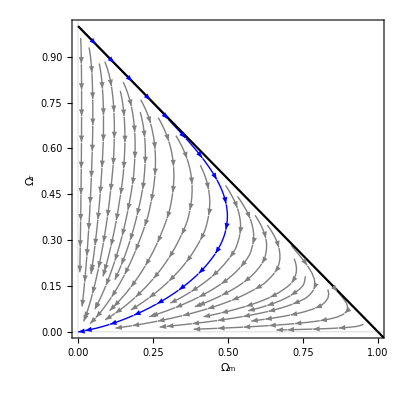

```mathematica
Show[StreamPlot[{Dx[x,y],Dy[x,y]},{x,0,1},{y,0,1},PlotRange->{{0,1},{0,1}},RegionFunction->Function[{x,y},x+y<1],PlotTheme->{"Scientific","Gray"},FrameLabel->{Style[Subscript[Ω, m],FontSize->16],Style[Subscript[Ω, r],FontSize->16]},FrameTicksStyle->13,RotateLabel->False,StreamStyle->Gray,StreamPoints->{{{{5/100,1-5/100-5/10000000},Blue},Automatic}}],Plot[1-x,{x,0,3/2},PlotTheme->{"Scientific","Gray"}]]
```

The solid black line corresponds to Ω_m+Ω_r=1 or, equivalently, Ω_Λ=0.  We see from the plot that if we have a universe composed of baryonic matter, radiation, and a small cosmological constant, this universe will evolve from a radiation-dominated period towards a matter-dominated one. After this period, the universe becomes dominated by the cosmological constant.

### Comments

• Although there is no time information on a phase plot, we can numerically integrate our differential equations to obtain this.

```mathematica
ODEsol[x0_,y0_]:=NDSolve[{x'[t]==x[t](3x[t]+4y[t]-3), y'[t]==y[t](3x[t]+4y[t]-4), x[0]==x0, y[0]==y0}, {x,y},{t,0,10}];
```

```mathematica
(*numerically solving the ODEs with the initial conditions of the blue trajectory*)
sol[1]=ODEsol[5/100,1-5/100-5/10000000];
```

```mathematica
fx=x/.sol[1][[1,1]];
fy = y/.sol[1][[1,2]];
```

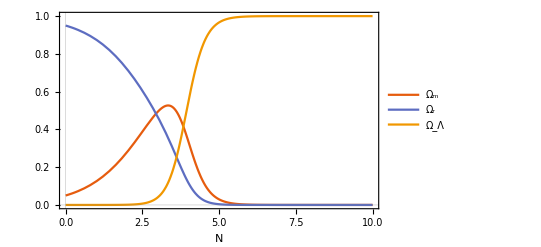

```mathematica
Plot[{fx[t],fy[t],1-(fx[t]+fy[t])},{t,0,10},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{Style["Ω_m",FontSize->18],Style["Ω_r",FontSize->18],Style["Ω_Λ",FontSize->18]},LegendFunction->(Framed[#,RoundingRadius->5,FrameStyle->{Gray,Thin}]&),LegendMargins->5],{After,Top}],FrameLabel->{Style["N",FontSize->16,FontWeight->Bold],None},FrameTicksStyle->13]
```

Here, we have the temporal evolution of the solution represented by the blue trajectory.  We also see how Ω_m,Ω_r,and Ω_Λ became constant around N = 6. This means that the blue trajectory has reached the fixed point by this time.

## Takeaway

• The method of dynamical systems is a useful tool for visualizing our solutions graphically and can serve as a supplement analysis for cosmological models.

## Main References

Bohmer, C. and Chan, N., Dynamical systems in cosmology (arxiv.org/abs/1409.5585)

Ryden, B., Introduction to Cosmology. Pearson Education Inc., New York, 2017

Carroll S., Spacetime and Geometry: An Introduction in General Relativity. Addison Wesley, 2004

## Extra slide: xAct derivation of the Friedmann equations in a spatially-flat universe

Credits to Reginald Bernardo in his lecture during the Gravity Group Workshop 2019

```mathematica
(*import xTensor and xCoba*)
<<xAct`xTensor`;
<<xAct`xCoba`;
(*optional*)
$CovDFormat="Prefix";
$PrePrint=ScreenDollarIndices;
Options[MakeRule];
Options[ContractMetric];

(*define manifold and metric*)
dimension=4;                                
DefManifold[M,dimension,{b,c,d,i,j,k,l,u,v}];
DefMetric[-1,g[-b,-c],CD,{";","∇"},WeightedWithBasis->AIndex];
PrintAs[RiemannCD]^="R"; PrintAs[RicciCD]^="R"; PrintAs[RicciScalarCD]^="R"; PrintAs[ChristoffelCD]^="Γ"; PrintAs[EinsteinCD]^="G";

(*define an xCoba chart*)
DefChart[B,M,{0,1,2,3},{t[],x[],y[],z[]}];

(*scale factor a(t) and the spatially flat FRW metric*)
DefScalarFunction[a];
frw={{-1,0,0,0},{0,a[t[]]^2,0,0},{0,0,a[t[]]^2,0},{0,0,0,a[t[]]^2}};

(*tell xCoba that frw is the metric and to compute the curvature quantities*)
MetricInBasis[g,-B,frw];
MetricCompute[g,B,All,CVSimplify->Simplify];
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2018, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.3, {2018,2,28}

CopyRight (C) 2002-2018, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.4, {2018,2,28}

CopyRight (C) 2005-2018, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

** DefTensor: Defining symmetric metric tensor g[-b,-c].

** DefTensor: Defining antisymmetric tensor epsilong[-b,-c,-d,-i].

** DefTensor: Defining tetrametric Tetrag[-b,-c,-d,-i].

** DefTensor: Defining tetrametric Tetrag†[-b,-c,-d,-i].

** DefCovD: Defining covariant derivative CD[-b].

** DefTensor: Defining vanishing torsion tensor TorsionCD[b,-c,-d].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[b,-c,-d].

** DefTensor: Defining Riemann tensor RiemannCD[-b,-c,-d,-i].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-b,-c].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-b,-c].

** DefTensor: Defining Weyl tensor WeylCD[-b,-c,-d,-i].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-b,-c].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining weight +2 density Detg[]. Determinant.

** DefChart: Defining chart B.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar x[].

** DefTensor: Defining coordinate scalar y[].

** DefTensor: Defining coordinate scalar z[].

** DefMapping: Defining mapping B.

** DefMapping: Defining inverse mapping iB.

** DefTensor: Defining mapping differential tensor diB[-a,iBb].

** DefTensor: Defining mapping differential tensor dB[-b,Ba].

** DefBasis: Defining basis B. Coordinated basis.

** DefCovD: Defining parallel derivative PDB[-b].

** DefTensor: Defining vanishing torsion tensor TorsionPDB[b,-c,-d].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDB[b,-c,-d].

** DefTensor: Defining vanishing Riemann tensor RiemannPDB[-b,-c,-d,i].

** DefTensor: Defining vanishing Ricci tensor RicciPDB[-b,-c].

** DefTensor: Defining antisymmetric +1 density etaUpB[b,c,d,i].

** DefTensor: Defining antisymmetric -1 density etaDownB[-b,-c,-d,-i].

** DefScalarFunction: Defining scalar function a.

Added independent rule g |   |  
0 | 0→-1 for tensor g

Added independent rule g |   |  
0 | 1→0 for tensor g

Added independent rule g |   |  
0 | 2→0 for tensor g

Added independent rule g |   |  
0 | 3→0 for tensor g

Added dependent rule g |   |  
1 | 0→g |   |  
0 | 1 for tensor g

Added independent rule g |   |  
1 | 1→a[t]^2 for tensor g

Added independent rule g |   |  
1 | 2→0 for tensor g

Added independent rule g |   |  
1 | 3→0 for tensor g

Added dependent rule g |   |  
2 | 0→g |   |  
0 | 2 for tensor g

Added dependent rule g |   |  
2 | 1→g |   |  
1 | 2 for tensor g

Added independent rule g |   |  
2 | 2→a[t]^2 for tensor g

Added independent rule g |   |  
2 | 3→0 for tensor g

Added dependent rule g |   |  
3 | 0→g |   |  
0 | 3 for tensor g

Added dependent rule g |   |  
3 | 1→g |   |  
1 | 3 for tensor g

Added dependent rule g |   |  
3 | 2→g |   |  
2 | 3 for tensor g

Added independent rule g |   |  
3 | 3→a[t]^2 for tensor g

** DefTensor: Defining weight +2 density DetgB[]. Determinant.

** DefTensor: Defining tensor ChristoffelCDPDB[b,-c,-d].

First off, we input the matter sources to the metric by first defining the tensor T and then assigning to this tensor the perfect fluid form in the chart B.

```mathematica
DefTensor[T[-b,-c],M,Symmetric[{-b,-c}]];
PF={{-ρ[t[]],0,0,0},{0,P[t[]],0,0},{0,0,P[t[]],0},{0,0,0,P[t[]]}};
ComponentValue[ComponentArray[T[{b,B},-{c,B}]],PF];

(*the perfect fluid*)
"(T^a)_b"==(T[b,-c]//ToBasis[B]//ComponentArray//ToValues//MatrixForm)
```

** DefTensor: Defining tensor T[-b,-c].

Added independent rule T | 0 |  
  | 0→-ρ[t] for tensor T

Added independent rule T | 0 |  
  | 1→0 for tensor T

Added independent rule T | 0 |  
  | 2→0 for tensor T

Added independent rule T | 0 |  
  | 3→0 for tensor T

Added dependent rule T | 1 |  
  | 0→T |   | 1
0 |   for tensor T

Added independent rule T |   | 1
0 |  →0 for tensor T

Added independent rule T | 1 |  
  | 1→P[t] for tensor T

Added independent rule T | 1 |  
  | 2→0 for tensor T

Added independent rule T | 1 |  
  | 3→0 for tensor T

Added dependent rule T | 2 |  
  | 0→T |   | 2
0 |   for tensor T

Added independent rule T |   | 2
0 |  →0 for tensor T

Added dependent rule T | 2 |  
  | 1→T |   | 2
1 |   for tensor T

Added independent rule T |   | 2
1 |  →0 for tensor T

Added independent rule T | 2 |  
  | 2→P[t] for tensor T

Added independent rule T | 2 |  
  | 3→0 for tensor T

Added dependent rule T | 3 |  
  | 0→T |   | 3
0 |   for tensor T

Added independent rule T |   | 3
0 |  →0 for tensor T

Added dependent rule T | 3 |  
  | 1→T |   | 3
1 |   for tensor T

Added independent rule T |   | 3
1 |  →0 for tensor T

Added dependent rule T | 3 |  
  | 2→T |   | 3
2 |   for tensor T

Added independent rule T |   | 3
2 |  →0 for tensor T

Added independent rule T | 3 |  
  | 3→P[t] for tensor T

(T^a)_b==(-ρ[t] | 0 | 0 | 0
0 | P[t] | 0 | 0
0 | 0 | P[t] | 0
0 | 0 | 0 | P[t])

The spatially-flat Friedman equations can be derived by equating the Einstein tensor to the perfect fluid stress-energy tensor.

```mathematica
(*compute up-down components of the Einstein tensor to match with the SET*)
ChangeComponents[EinsteinCD[{b,B},-{c,B}],EinsteinCD[-{b,B},-{c,B}]];
```

Added independent rule G | 0 |  
  | 0→G |   |  
0 | 0 g | 0 | 0
  |  +G |   |  
0 | 1 g | 0 | 1
  |  +G |   |  
0 | 2 g | 0 | 2
  |  +G |   |  
0 | 3 g | 0 | 3
  |   for tensor EinsteinCD

Added independent rule G | 0 |  
  | 1→G |   |  
0 | 1 g | 0 | 0
  |  +G |   |  
1 | 1 g | 0 | 1
  |  +G |   |  
1 | 2 g | 0 | 2
  |  +G |   |  
1 | 3 g | 0 | 3
  |   for tensor EinsteinCD

Added independent rule G | 0 |  
  | 2→G |   |  
0 | 2 g | 0 | 0
  |  +G |   |  
1 | 2 g | 0 | 1
  |  +G |   |  
2 | 2 g | 0 | 2
  |  +G |   |  
2 | 3 g | 0 | 3
  |   for tensor EinsteinCD

Added independent rule G | 0 |  
  | 3→G |   |  
0 | 3 g | 0 | 0
  |  +G |   |  
1 | 3 g | 0 | 1
  |  +G |   |  
2 | 3 g | 0 | 2
  |  +G |   |  
3 | 3 g | 0 | 3
  |   for tensor EinsteinCD

Added dependent rule G | 1 |  
  | 0→G |   | 1
0 |   for tensor EinsteinCD

Added independent rule G |   | 1
0 |  →G |   |  
0 | 0 g | 0 | 1
  |  +G |   |  
0 | 1 g | 1 | 1
  |  +G |   |  
0 | 2 g | 1 | 2
  |  +G |   |  
0 | 3 g | 1 | 3
  |   for tensor EinsteinCD

Added independent rule G | 1 |  
  | 1→G |   |  
0 | 1 g | 0 | 1
  |  +G |   |  
1 | 1 g | 1 | 1
  |  +G |   |  
1 | 2 g | 1 | 2
  |  +G |   |  
1 | 3 g | 1 | 3
  |   for tensor EinsteinCD

Added independent rule G | 1 |  
  | 2→G |   |  
0 | 2 g | 0 | 1
  |  +G |   |  
1 | 2 g | 1 | 1
  |  +G |   |  
2 | 2 g | 1 | 2
  |  +G |   |  
2 | 3 g | 1 | 3
  |   for tensor EinsteinCD

Added independent rule G | 1 |  
  | 3→G |   |  
0 | 3 g | 0 | 1
  |  +G |   |  
1 | 3 g | 1 | 1
  |  +G |   |  
2 | 3 g | 1 | 2
  |  +G |   |  
3 | 3 g | 1 | 3
  |   for tensor EinsteinCD

Added dependent rule G | 2 |  
  | 0→G |   | 2
0 |   for tensor EinsteinCD

Added independent rule G |   | 2
0 |  →G |   |  
0 | 0 g | 0 | 2
  |  +G |   |  
0 | 1 g | 1 | 2
  |  +G |   |  
0 | 2 g | 2 | 2
  |  +G |   |  
0 | 3 g | 2 | 3
  |   for tensor EinsteinCD

Added dependent rule G | 2 |  
  | 1→G |   | 2
1 |   for tensor EinsteinCD

Added independent rule G |   | 2
1 |  →G |   |  
0 | 1 g | 0 | 2
  |  +G |   |  
1 | 1 g | 1 | 2
  |  +G |   |  
1 | 2 g | 2 | 2
  |  +G |   |  
1 | 3 g | 2 | 3
  |   for tensor EinsteinCD

Added independent rule G | 2 |  
  | 2→G |   |  
0 | 2 g | 0 | 2
  |  +G |   |  
1 | 2 g | 1 | 2
  |  +G |   |  
2 | 2 g | 2 | 2
  |  +G |   |  
2 | 3 g | 2 | 3
  |   for tensor EinsteinCD

Added independent rule G | 2 |  
  | 3→G |   |  
0 | 3 g | 0 | 2
  |  +G |   |  
1 | 3 g | 1 | 2
  |  +G |   |  
2 | 3 g | 2 | 2
  |  +G |   |  
3 | 3 g | 2 | 3
  |   for tensor EinsteinCD

Added dependent rule G | 3 |  
  | 0→G |   | 3
0 |   for tensor EinsteinCD

Added independent rule G |   | 3
0 |  →G |   |  
0 | 0 g | 0 | 3
  |  +G |   |  
0 | 1 g | 1 | 3
  |  +G |   |  
0 | 2 g | 2 | 3
  |  +G |   |  
0 | 3 g | 3 | 3
  |   for tensor EinsteinCD

Added dependent rule G | 3 |  
  | 1→G |   | 3
1 |   for tensor EinsteinCD

Added independent rule G |   | 3
1 |  →G |   |  
0 | 1 g | 0 | 3
  |  +G |   |  
1 | 1 g | 1 | 3
  |  +G |   |  
1 | 2 g | 2 | 3
  |  +G |   |  
1 | 3 g | 3 | 3
  |   for tensor EinsteinCD

Added dependent rule G | 3 |  
  | 2→G |   | 3
2 |   for tensor EinsteinCD

Added independent rule G |   | 3
2 |  →G |   |  
0 | 2 g | 0 | 3
  |  +G |   |  
1 | 2 g | 1 | 3
  |  +G |   |  
2 | 2 g | 2 | 3
  |  +G |   |  
2 | 3 g | 3 | 3
  |   for tensor EinsteinCD

Added independent rule G | 3 |  
  | 3→G |   |  
0 | 3 g | 0 | 3
  |  +G |   |  
1 | 3 g | 1 | 3
  |  +G |   |  
2 | 3 g | 2 | 3
  |  +G |   |  
3 | 3 g | 3 | 3
  |   for tensor EinsteinCD

Added dependent rule G |   | 0
0 |  →G | 0 |  
  | 0 for tensor EinsteinCD

Added dependent rule G |   | 0
1 |  →G | 0 |  
  | 1 for tensor EinsteinCD

Added dependent rule G |   | 1
1 |  →G | 1 |  
  | 1 for tensor EinsteinCD

Added dependent rule G |   | 0
2 |  →G | 0 |  
  | 2 for tensor EinsteinCD

Added dependent rule G |   | 1
2 |  →G | 1 |  
  | 2 for tensor EinsteinCD

Added dependent rule G |   | 2
2 |  →G | 2 |  
  | 2 for tensor EinsteinCD

Added dependent rule G |   | 0
3 |  →G | 0 |  
  | 3 for tensor EinsteinCD

Added dependent rule G |   | 1
3 |  →G | 1 |  
  | 3 for tensor EinsteinCD

Added dependent rule G |   | 2
3 |  →G | 2 |  
  | 3 for tensor EinsteinCD

Added dependent rule G |   | 3
3 |  →G | 3 |  
  | 3 for tensor EinsteinCD

Computed G | b |  
  | c→G |   |  
d | c g | b | d
  |   in 2.264942 Seconds

Finally, we obtain the Friedman equations from the following.

```mathematica
LHS=(EinsteinCD[b,-c]//ToBasis[B]//ComponentArray//ToValues//ToValues);
RHS=(8π T[b,-c]//ToBasis[B]//ComponentArray//ToValues);

(*Friedman equations*)
(LHS//MatrixForm)==(RHS//MatrixForm)
```

(-(3 a'[t]^2)/a[t]^2 | 0 | 0 | 0
0 | (-a'[t]^2-2 a[t] a''[t])/a[t]^2 | 0 | 0
0 | 0 | (-a'[t]^2-2 a[t] a''[t])/a[t]^2 | 0
0 | 0 | 0 | (-a'[t]^2-2 a[t] a''[t])/a[t]^2)==(-8 π ρ[t] | 0 | 0 | 0
0 | 8 π P[t] | 0 | 0
0 | 0 | 8 π P[t] | 0
0 | 0 | 0 | 8 π P[t])

The independent equations from the above are...

```mathematica
removebrackets=t[]->t;

(*first Friedman equation*)
friedman1=(LHS[[1,1]]/.removebrackets)==(RHS[[1,1]]/.removebrackets)

(*second Friedman equation*)
friedman2=(LHS[[2,2]]/.removebrackets)==(RHS[[2,2]]/.removebrackets)
```

-(3 a'[t]^2)/a[t]^2==-8 π ρ[t]

(-a'[t]^2-2 a[t] a''[t])/a[t]^2==8 π P[t]

Typically, we express the Friedmann equations in terms of the Hubble parameter H=a'/a. We can obtain the Friedman equations in terms of the Hubble parameter by imposing the following rules.

```mathematica
AtoHubble=Solve[{H[t]==a'[t]/a[t],H'[t]==D[a'[t]/a[t],t]},{a'[t],a''[t]}][[1]];
```

In terms of the Hubble parameter, the Friedmann equations are given by the following.

```mathematica
friedman1/.AtoHubble//Simplify
friedman2/.AtoHubble//Simplify
```

3 H[t]^2==8 π ρ[t]

3 H[t]^2+8 π P[t]+2 H'[t]==0